More about Numbers

When you do a computation with whole numbers, the Wolfram Language gives you an exact answer. It does the same with exact fractions.

Adding 1/2+1/3 gives an exact answer as a fraction:

```mathematica
1/2+1/3
```

5/6

Often you’ll just want a numerical or decimal approximation. You can get that using the function N (for “numerical”).

Get an approximate numerical answer:

```mathematica
N[1/2+1/3]
```

0.833333

If there’s any decimal number in your input, the Wolfram Language will automatically give you an approximate answer.

The presence of a decimal number makes the result be approximate:

```mathematica
1.8/2+1/3
```

1.23333

It’s enough just to have a decimal point at the end of a number:

```mathematica
1/2.+1/3
```

0.833333

The Wolfram Language can handle numbers of any size, at least so long as they fit in your computer’s memory.

Here’s 2 raised to the power 1000:

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

Get a numerical approximation:

```mathematica
N[2^1000]
```

1.07151×10^301

This approximate form is given in scientific notation. If you need to enter scientific notation, you can do it with *^.

Enter a number in scientific notation:

```mathematica
2.7*^6
```

2.7×10^6

Commonly used numbers like π (pi) are built into the Wolfram Language.

Get a numerical approximation to π:

```mathematica
N[Pi]
```

3.14159

The Wolfram Language can compute to arbitrary precision, so for example it can find millions of digits of π if you want them.

Compute 250 digits of π:

```mathematica
N[Pi,250]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

There are many functions in the Wolfram Language that handle integers (whole numbers). There are also many functions that handle real numbers—approximate numbers with decimals. An example is RandomReal, which gives random real numbers.

Generate a random real number in the range 0 to 10:

```mathematica
RandomReal[10]
```

2.08658

Generate 5 random real numbers:

```mathematica
Table[RandomReal[10],5]
```

{4.15071,4.81048,8.82945,9.84995,9.08313}

An alternative way to ask for 5 random real numbers:

```mathematica
RandomReal[10,5]
```

{6.47318,3.29181,3.57615,8.11204,3.38286}

Random real numbers in the range 20 to 30:

```mathematica
RandomReal[{20,30},5]
```

{24.1202,20.1288,20.393,25.6455,20.9268}

The Wolfram Language has a huge range of mathematical functions built in, from basic to very sophisticated.

Find the 100th prime number:

```mathematica
Prime[100]
```

541

Find the millionth prime number:

```mathematica
Prime[1000000]
```

15485863

Plot the first 50 primes:

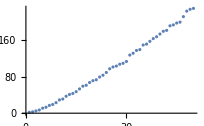

```mathematica
ListPlot[Table[Prime[n],{n,50}]]
```

Three functions common in many practical situations are Sqrt (square root), Log10 (logarithm to base 10) and Log (natural logarithm).

The square root of 16 is 4:

```mathematica
Sqrt[16]
```

4

If you don’t ask for a numerical approximation, you’ll get an exact formula:

```mathematica
Sqrt[200]
```

10 √2

N gives a numerical approximation:

```mathematica
N[Sqrt[200]]
```

14.1421

Logarithms are often useful when you’re dealing with numbers that have a wide range of sizes. Let’s plot the masses of the planets. With ListPlot one can’t tell anything about the planets before Jupiter. But ListLogPlot shows the relative sizes much more clearly.

Make an ordinary ListPlot of the masses of the planets:

```mathematica
ListPlot[EntityClass["Planet",All]["Mass"]]
```

-Graphics-

Make a log plot:

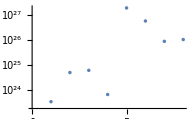

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

There are a few more functions that show up frequently in general programming. First, there’s the almost trivial function Abs, that finds the absolute value, or positive part, of a number.

Abs effectively just drops minus signs:

```mathematica
{Abs[3],Abs[-3]}
```

{3,3}

Next there’s Round, which rounds to the nearest whole number.

Round rounds to the nearest whole number:

```mathematica
{Round[3.2],Round[3.4],Round[3.6],Round[3.9]}
```

{3,3,4,4}

Another function that’s very useful is Mod. Let’s say you’re counting up minutes in an hour. When you reach 60, you’ll want to start again from 0. That’s what Mod lets you do.

Compute a sequence of numbers mod 60:

```mathematica
{Mod[50,60],Mod[55,60],Mod[60,60],Mod[65,60],Mod[70,60]}
```

{50,55,0,5,10}

Vocabulary

N[expr] |   | numerical approximation 
Pi |   | the number π (pi)≃3.14 
Sqrt[x] |   | square root 
Log10[x] |   | logarithm to base 10 
Log[x] |   | natural logarithm (ln) 
Abs[x] |   | absolute value (drop minus signs) 
Round[x] |   | round to nearest integer 
Prime[n] |   | nth prime number
Mod[x,n] |   | modulo (“clock arithmetic”) 
RandomReal[max] |   | random real number between 0 and max 
RandomReal[max,n] |   | list of n random real numbers
ListLogPlot[data] |   | plot on a logarithmic scale

"14 Exercises Available"
"with 4 extras" | "Get Started »"

Find √2 to 500-digit precision. »

| Expected output: |  
  | 1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372 |

Generate 10 random real numbers between 0 and 1. »

| Sample expected output: |  
  | {0.981757,0.501571,0.0805282,0.0247074,0.0663221,0.812191,0.929721,0.949164,0.674154,0.0702841} |

Make a plot of 200 points with random real x and y coordinates between 0 and 1. »

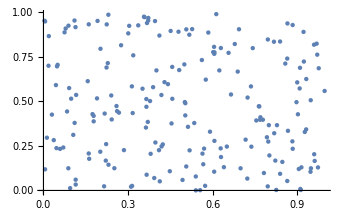
| Sample expected output: |  
  | -Graphics- |

Create a random walk using AnglePath and 1000 random real numbers between 0 and 2π. »

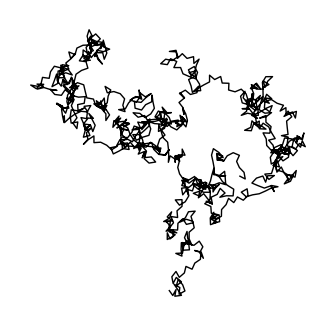
| Sample expected output: |  
  | -Graphics- |

Make a table of Mod[n^2,10] for n from 0 to 30. »

| Expected output: |  
  | {0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0} |

Make a line plot of Mod[n^n,10] for n from 1 to 100. »

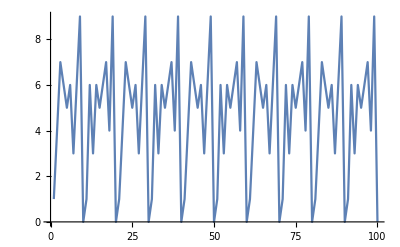
| Expected output: |  
  | -Graphics- |

Make a table of the first 10 powers of π, rounded to integers. »

| Expected output: |  
  | {3,10,31,97,306,961,3020,9489,29809,93648} |

Make a graph by connecting n with Mod[n^2,100] for n from 0 to 99. »

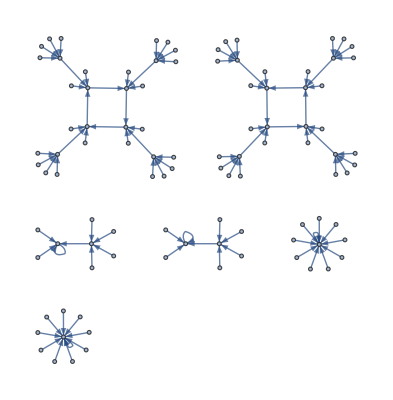
| Expected output: |  
  | -Graphics- |

Generate graphics of 50 circles with random real coordinates 0 to 10, random real radii from 0 to 2, and random colors. »

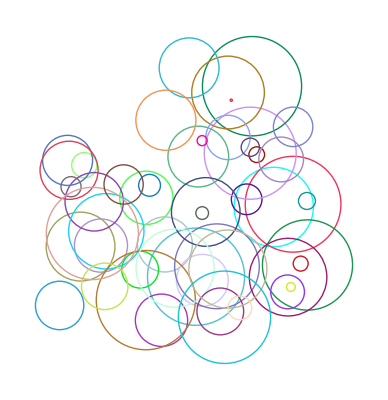
| Sample expected output: |  
  | -Graphics- |

Make a plot of the nth prime divided by n*log(n), for n from 2 to 1000. »

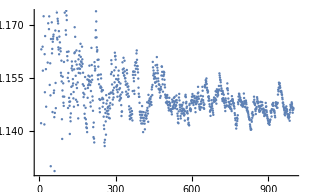
| Expected output: |  
  | -Graphics- |

Make a line plot of the differences between successive primes up to 100. »

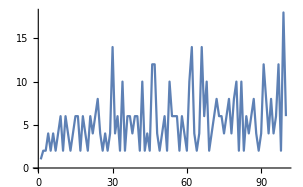
| Expected output: |  
  | -Graphics- |

Generate a sequence of 20 middle C notes with random durations between 0 and 0.5 seconds. »

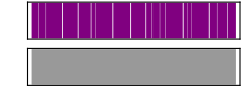
| Sample expected output: |  
  | -Graphics- |

Make an array plot of Mod[i,j] for i and j up to 50. »

| Expected output: |  
  | -Graphics- |

Make a list for n from 2 to 10 of array plots for x and y up to 50 of x^y mod n. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use Round to compute the fractional part of π to 50 digits. »

| Expected output: |  
  | 0.14159265358979323846264338327950288419716939937511 |

Find the sum of the first 1000 prime numbers. »

| Expected output: |  
  | 3682913 |

Make a list of the first 100 primes modulo 4. »

| Expected output: |  
  | {2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1} |

Make a list of the first 10000 primes modulo 4, multiply them by 90° and create an angle path from them. »

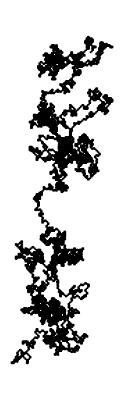
| Expected output: |  
  | -Graphics- |

Q&A

What are examples of mathematical functions in the Wolfram Language?

From standard school math, ones like Sin, Cos, ArcTan, Exp, as well as GCD, Factorial, Fibonacci. From physics and engineering and higher math, ones like Gamma (“gamma function”), BesselJ (“Bessel function”), EllipticK (“elliptic integral”), Zeta (“Riemann zeta function”), PrimePi, EulerPhi. From statistics, ones like Erf, NormalDistribution, ChiSquareDistribution. Hundreds of functions altogether.

What is the precision of a number?

It’s the total number of decimal digits quoted in the number. N[100/3,5] gives 33.333, which has 5 digits of precision. The number 100/3 is exact; N[100/3,5] approximates it to 5-digit precision.

What does the  at the end of each line in a long number mean?

It’s there to show that the number continues onto the next line—like a hyphen in text.

Can I work with numbers in bases other than 10?

Yes. Enter a number in base 16 as 16^^ffa5. Find digits using IntegerDigits[655,16].

Can the Wolfram Language handle complex numbers?

Of course. The symbol I (capital “i”) represents the square root of −1.

Why does N[1.5/7,100] not give me a 100-digit result?

Because 1.5 is an approximate number with much less than 100-digit precision. N[15/70,100] will for example give a 100-digit-precision number.

Tech Notes

The Wolfram Language does “arbitrary-precision computation”, meaning that it can keep as many digits in a number as you want.

When you generate a number with a certain precision using N, the Wolfram Language will automatically keep track of how that precision is affected by computations—so you don’t have to do your own numerical analysis of roundoff errors.

If you type a number like 1.5, it’s assumed to be at the native “machine precision” of numbers on your computer (usually about 16 digits, though only 6 are usually displayed). Use 1.5`100 to specify 100-digit precision.

With exact input (like 4 or 2/3 or Pi), the Wolfram Language always tries to give exact output. But if the input contains an approximate number (like 2.3), or if you use N, it’ll use numerical approximation.

Numerical approximation is often crucial in making large-scale computations feasible.

PrimeQ tests if a number is prime (see Section 28). FactorInteger finds the factors of an integer.

RandomReal can give numbers that aren’t just uniformly distributed. For example, RandomReal[NormalDistribution[ ]] gives normally distributed numbers.

Round rounds to the nearest integer (up or down); Floor always rounds down; Ceiling always rounds up.

RealDigits is the analog of IntegerDigits for real numbers.

More to Explore

Guide to Numbers in the Wolfram Language »

Guide to Mathematical Functions in the Wolfram Language »